```mathematica
z = x + Sqrt[-1]*y
```

x+ⅈ y

Abs[1+x+ⅈ y]<1

{x,-2,1}

{y,-1.5,1.5}

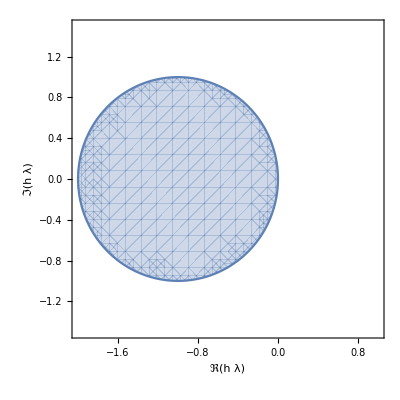

```mathematica
R = Abs[1+z]<1
xbox = {x,-2,1}
ybox = {y, -1.5, 1.5}
Show[RegionPlot[R, xbox, ybox, Axes->True, AxesLabel->{ToExpression["\\Re(h\\lambda)",TeXForm,HoldForm],ToExpression["\\Im(h\\lambda)",TeXForm,HoldForm]}], PlotLabel->None, LabelStyle->{18, GrayLevel[0]}]
```

Abs[1-x-ⅈ y]>1

{x,-1,2}

{y,-1.5,1.5}

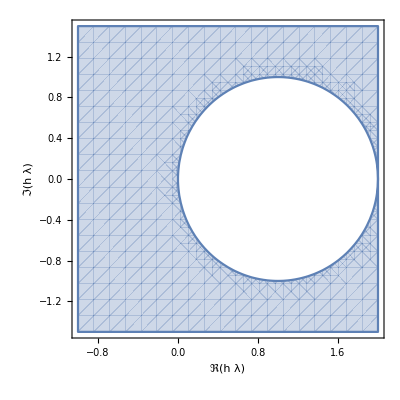

```mathematica
R = Abs[1-z]>1
xbox = {x,-1,2}
ybox = {y, -1.5,1.5}
Show[RegionPlot[R, xbox, ybox, Axes->True, AxesLabel->{ToExpression["\\Re(h\\lambda)",TeXForm,HoldForm],ToExpression["\\Im(h\\lambda)",TeXForm,HoldForm]}], PlotLabel->None, LabelStyle->{18, GrayLevel[0]}]
```

Abs[(2+x+ⅈ y)/(2-x-ⅈ y)]<1

{x,-2,2}

{y,-2,2}

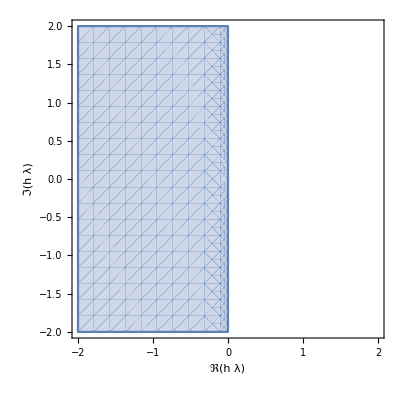

```mathematica
R = Abs[(2+z)/(2-z)]<1
xbox = {x,-2,2}
ybox = {y,-2,2}
Show[RegionPlot[R, xbox, ybox, Axes->True, AxesLabel->{ToExpression["\\Re(h\\lambda)",TeXForm,HoldForm],ToExpression["\\Im(h\\lambda)",TeXForm,HoldForm]}], PlotLabel->None, LabelStyle->{18, GrayLevel[0]}]
```